```mathematica
M=GovernMat2[QW];
```

```mathematica
v=L2V[QW,rho01];
QWPADETimeList = List[];
QWPADEErrorList=List[];
QWSSTimeList = List[];
QWSSErrorList=List[];
QWKryTimeList = List[];
QWKryErrorList=List[];
Do[
(*t=Power[2,i];*)
MM=N[M]*t;
qwexact=MatrixExp[M*t];
qwexactv=MatrixExp[M*t,Flatten[v]];
qwPade=AbsoluteTiming[MatrixExp[MM,Method->Pade]];
qwSS=AbsoluteTiming[ExpSS[MM]];
qwKry=AbsoluteTiming[MatrixExp[MM,Flatten[v],Method->"Krylov"]];
AppendTo[QWPADETimeList,qwPade[[1]]];
AppendTo[QWPADEErrorList,Abs[Max[qwPade[[2]]-qwexact]]];
AppendTo[QWSSTimeList,qwSS[[1]]];
AppendTo[QWSSErrorList,Abs[Max[qwSS[[2]]-qwexact]]];
AppendTo[QWKryTimeList,qwKry[[1]]];
AppendTo[QWKryErrorList,Abs[Max[qwKry[[2]]-qwexactv]]];
,{t,1,50}]
```

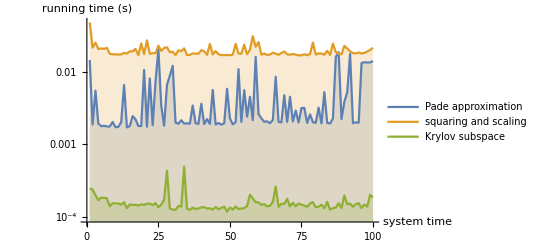

```mathematica
QWTime=ListLinePlot[{QWPADETimeList,QWSSTimeList,QWKryTimeList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"system time","running time (s)"},ScalingFunctions->"Log"]
```

```mathematica
Export["C:\\Users\\mei\\Desktop\\QCTMC\\QWTime.eps",QWTime]
```

C:\Users\mei\Desktop\QCTMC\QWTime.eps

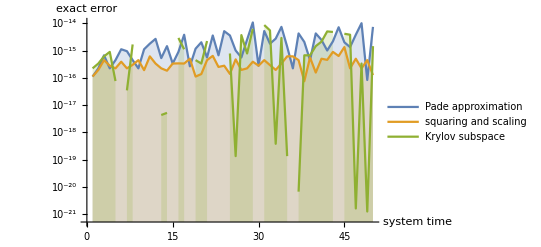

```mathematica
QWError=ListLinePlot[{QWPADEErrorList,QWSSErrorList,QWKryErrorList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"system time","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export["C:\\Users\\mei\\Desktop\\QCTMC\\QWError.eps",QWError]
```

C:\Users\mei\Desktop\QCTMC\QWError.eps

```mathematica
(*Runtime only*)
v=L2V[QW,rho01];
QWPADETimeList = List[];
QWSSTimeList = List[];
QWKryTimeList = List[];
Do[
(*t=Power[2,i];*)
MM=N[M]*t;
qwPade=AbsoluteTiming[MatrixExp[MM,Method->Pade]];
qwSS=AbsoluteTiming[ExpSS[MM]];
qwKry=AbsoluteTiming[MatrixExp[MM,Flatten[v],Method->"Krylov"]];
AppendTo[QWPADETimeList,qwPade[[1]]];
AppendTo[QWSSTimeList,qwSS[[1]]];
AppendTo[QWKryTimeList,qwKry[[1]]];
,{t,1,1000,10}]
```